```mathematica
terminals={"a","b","c","d","e","f","g","h"}
nonTerminals={"A","B","C","D"}
functions={f,g,h,i}
initSentence=g["A"]...~~"B"
(*... indicates zero or more g["A"]*)rules={"A":>"a","B":>"b"|"c"|"d",(*immediately choose any terminal of the rhs*)"C":>"e"|"f","D":>"g"|"h","A":>"a"~~"b","A":>"A"~~"a","A":>"B"~~"b","A":>f["e"|"f"]~~"a",(*do not evaluate f but choose "e" or "f"*)"A":>g@"h"~~"C","B":>g@"C",(*do not evaluate g but "C" must be replaced later*)"B":>"B"~~h@"e","C":>f@"f","C":>"C"~~g@"d"}
```

{a,b,c,d,e,f,g,h}

{A,B,C,D}

{f,g,h,i}

g[A]...~~B

{A:>a,B:>b|c|d,C:>e|f,D:>g|h,A:>a~~b,A:>A~~a,A:>B~~b,A:>f[e|f]~~a,A:>g[h]~~C,B:>g[C],B:>B~~h[e],C:>f[f],C:>C~~g[d]}

```mathematica
g["A"]...~~"B"                 (*initial sentence*)
g["A"] g["A"]~~"B"              (*g["A"] is repeated randomly*)
g["A"~~"a"] g["A"]~~"B"       (*rule A ":>"A "~~"a " is applied *)
g["A"~~"a"] g[g@"C"]~~"B"     (*rule "B":>g@"C" is applied*)
g["a"~~"a"] g[g@"C"]~~"B"     (*rule "A":>"a" is applied*)
g["a"~~"a"] g[g@f@"f"]~~"B"   (*rule "C":>f@"f" is applied*)
g["a"~~"a"] g[g@f@"f"]~~"b"|"c"|"d"  (*rule "B":>"b"|"c"|"d" is applied*)
g["a"~~"a"] g[g@f@"f"]~~"d"   (*one terminal is randomly chosen*)
(*terminate and evaluate g f*)
```

g[A]...~~B

g[A]^2~~B

g[A] g[Aa]~~B

g[Aa] g[g[C]]~~B

g[aa] g[g[C]]~~B

g[aa] g[g[f[f]]]~~B

g[aa] g[g[f[f]]]~~b|c|d

g[aa] g[g[f[f]]]~~d

```mathematica
ClearAll[randomSentence,randomCount]
randomCount[]:=RandomVariate[GeometricDistribution[0.5]]
SetAttributes[randomSentence,HoldAll]
randomSentence[rules_,expr_]:=Module[{generate},SetAttributes[generate,HoldAll];Replace[#[[1,1]]:>#&/@GatherBy[rules,First],(_:>r_):>r,{3}]/.(a_:>{b___}):>(generate[a]:=generate[Alternatives[b]]);generate[a_Alternatives]:=generate@@RandomChoice[List@@Hold/@Unevaluated@a];generate[(r:(Repeated|RepeatedNull))[e_]]:=Hold@@Evaluate@ConstantArray[0,randomCount[]+Boole[r===Repeated]]/.0:>generate[e]/.Hold->Composition[generate,List];generate[l_List]:=StringJoin@@generate/@Unevaluated@l;generate[x:_[___]]:=generate/@Unevaluated@x;generate[x_]:=x;generate[expr]]
```

```mathematica
ClearAll[f,g,h,i]
f[x___]:=x<>"er";
g[x___]:=x<>"ed";
h[x___]:=x<>"ing";
i[x___]:=x<>"y";

$rules={"Species":>"Animal"|"Plant","Species":>f@"Action","Species":>{"Color"|"Type","-","Species"},"Attribute":>"Type"|"Color","Attribute":>{"Animal","-",f@"Action"},"Attribute":>{"Color"|"Type","-",g@"Part"},"Attribute":>i@"Plant","Attribute":>{"Plant"|"Animal","-",h@"Action"},"Animal":>"warble"|"shrew"|"whale"|"caiman"|"babuin"|"bat"|"bug","Plant":>"bush"|"moss"|"fern"|"grass"|"squash"|"seed","Part":>"back"|"head"|"finger"|"tail"|"ear"|"wing"|"thorn","Color":>"black"|"red"|"white"|"blue"|"silver"|"crimson"|"dark","Type":>"long"|"cross"|"sharp"|"thick"|"heavy"|"fluffy"|"big"|"wild","Action":>"jump"|"kill"|"stalk"|"sting"|"climb"|"crawl"|"eat"};
```

```mathematica
Table[randomSentence[$rules,{{"Attribute"," "}...,"Species"}],{10}]//Column
```

dark-eared climber
bushy white climber
fluffy-crawler
bug-stinger bug-killer black-stalker
warble-climber squash
jumper
killer
seedy whale
caiman
blue bush

```mathematica
Table[randomSentence[$rules,{{"Attribute"," "}...,"Species"}],{10}]//Column
```

bug-stalker stalker
caiman
wild-thorned babuin-stalker sharp-white-climber
seedy caiman
bat-eater jumper
seed
warble-jumping squashy babuin-crawler stinger
crimson-jumper
jumper
squash-stinging jumper

```mathematica
Clear[$rules, randomCount, randomSentence, f,h,i,g,terminals, nonTerminals, functions, initSentence, rules]
```

```mathematica
Clear[Table]
```

Clear::wrsym: Symbol Table is Protected.

```mathematica
f[x___]:=x<>"er"
g[x___]:=x<>"ed"
h[x___]:=x<>"ing"
i[x___]:=x<>"y"
```

```mathematica
terminals={"a","b","c","d","e","f","g","h"};
nonTerminals={"A","B","C","D"};
functions={f,g,h,i};

initSentence=g["A"]...~~"B";(*... indicates zero or more g["A"]*)rules={"A":>"a","B":>"b"|"c"|"d",(*immediately choose any terminal of the rhs*)"C":>"e"|"f","D":>"g"|"h","A":>"a"~~"b","A":>"A"~~"a","A":>"B"~~"b","A":>f["e"|"f"]~~"a",(*do not evaluate f but choose "e" or "f"*)"A":>g@"h"~~"C","B":>g@"C",(*do not evaluate g but "C" must be replaced later*)"B":>"B"~~h@"e","C":>f@"f","C":>"C"~~g@"d"};
```

```mathematica
{"a","b","c","d","e","f","g","h"}
```

{a,b,c,d,e,f,g,h}

```mathematica
g["A"]...~~"B"                 (*initial sentence*)
g["A"] g["A"]~~"B"              (*g["A"] is repeated randomly*)
g["A"~~"a"] g["A"]~~"B"       (*rule A ":>"A "~~"a " is applied *)
g["A"~~"a"] g[g@"C"]~~"B"     (*rule "B":>g@"C" is applied*)
g["a"~~"a"] g[g@"C"]~~"B"     (*rule "A":>"a" is applied*)
g["a"~~"a"] g[g@f@"f"]~~"B"   (*rule "C":>f@"f" is applied*)
g["a"~~"a"] g[g@f@"f"]~~"b"|"c"|"d"  (*rule "B":>"b"|"c"|"d" is applied*)
g["a"~~"a"] g[g@f@"f"]~~"d"   (*one terminal is randomly chosen*)
(*terminate and evaluate g,f*)
```

Aed...~~B

Aed^2~~B

Aaed Aed~~B

Aaed Ceded~~B

aaed Ceded~~B

aaed fereded~~B

aaed fereded~~b|c|d

aaed fereded~~d

```mathematica
:>
```

```mathematica
Information[:>]
```

```mathematica
citiesGrammar=CloudDeploy[GrammarRules[{cs:DelimitedSequence[GrammarToken["City"],","|";"|"and"]:>cs}]]
```

CloudObject[https://www.wolframcloud.com/objects/0167111b-665b-44f3-8677-ebb06c21fadc]

```mathematica
CloudDeploy[1+1]
```

CloudObject[https://www.wolframcloud.com/objects/963096d0-c94e-4894-a2e9-da387f201cc2]

```mathematica
SystemOpen[CloudObject["https://www.wolframcloud.com/objects/963096d0-c94e-4894-a2e9-da387f201cc2"]⟦1⟧]
```

```mathematica
GrammarApply[citiesGrammar,"Saint Louis; New York, LA and Dallas"]
```

{Saint Louis,New York City,Los Angeles,Dallas}

```mathematica
GrammarRules[{cs:DelimitedSequence[GrammarToken["City"],","|";"|"and"]:>cs}]
```

GrammarRules[{cs:DelimitedSequence[GrammarToken[City],,|;|and]:>cs}]

```mathematica
CloudDeploy[GrammarRules[{cs:DelimitedSequence[GrammarToken["City"],","|";"|"and"]:>cs}]]
```

CloudObject[https://www.wolframcloud.com/objects/00055875-47b4-4751-985d-4b87ac0fa059]

```mathematica
routeGrammar=CloudDeploy[GrammarRules[{GrammarToken["Route"],GrammarToken["Origin"],GrammarToken["Destination"]},{"Route"->AnyOrder[start:GrammarToken["Origin"],end:GrammarToken["Destination"]]:>(start->end),"Origin"->FixedOrder["from",loc:GrammarToken["City"]]:>loc,"Destination"->FixedOrder["to",loc:GrammarToken["City"]]:>loc}]]
```

WolframAlpha::creditlimit: -- Message text not found --

$Failed

```mathematica
StringReplaceList["12345", {"1"->"11","2"->"22"}]
```

{112345,122345}

```mathematica
s="S";
Do[s=Select[Flatten[Map[StringReplaceList[s,#]&,{"S"->"aBSc","S"->"abc","Ba"->"aB","Bb"->"bb"}]],StringLength[#]<7&];
If[s=={},Break[]];
Print[s];,{10}]
```

{aBSc,abc}

{aBabcc}

{aaBbcc}

{aabbcc}

```mathematica
init="S";
While[init≠"aabbcc",transforms={};
res=FixedPointList[StringReplace[#,(r=RandomChoice[rules];transforms={transforms,r};r),1]&,"S",10];
init=res//Last];
res//Most
transforms//Flatten//Most
```

$Aborted

{S}

Most::nomost: Cannot take Most of expression {} with length zero.

Most[{}]

```mathematica
StringReplaceList["11111111", "1"->"lol"]
```

{lol1111111,1lol111111,11lol11111,111lol1111,1111lol111,11111lol11,111111lol1,1111111lol}

```mathematica
f@x
```

StringJoin::string: String expected at position 1 in x<>er.

x<>er

```mathematica
Clear[f,g,h,i]
```

```mathematica
f@@x
```

x

```mathematica
f@@@x
```

x

```mathematica
f@*g
```

f@*g

```mathematica
f@*g@*h@x
```

f[g[h[x]]]

```mathematica
f@g@h@x
```

f[g[h[x]]]

```mathematica
Construct[f,x,y,z]
```

f[x,y,z]

```mathematica
Construct[f,x]
```

f[x]

```mathematica
Outer[Construct,{f1,f2,f3},{x1,x2},{y1,y2,y3}]
```

{{{f1[x1,y1],f1[x1,y2],f1[x1,y3]},{f1[x2,y1],f1[x2,y2],f1[x2,y3]}},{{f2[x1,y1],f2[x1,y2],f2[x1,y3]},{f2[x2,y1],f2[x2,y2],f2[x2,y3]}},{{f3[x1,y1],f3[x1,y2],f3[x1,y3]},{f3[x2,y1],f3[x2,y2],f3[x2,y3]}}}

```mathematica
Outer[f,Range[10],Range[10]]
```

{{f[1,1],f[1,2],f[1,3],f[1,4],f[1,5],f[1,6],f[1,7],f[1,8],f[1,9],f[1,10]},{f[2,1],f[2,2],f[2,3],f[2,4],f[2,5],f[2,6],f[2,7],f[2,8],f[2,9],f[2,10]},{f[3,1],f[3,2],f[3,3],f[3,4],f[3,5],f[3,6],f[3,7],f[3,8],f[3,9],f[3,10]},{f[4,1],f[4,2],f[4,3],f[4,4],f[4,5],f[4,6],f[4,7],f[4,8],f[4,9],f[4,10]},{f[5,1],f[5,2],f[5,3],f[5,4],f[5,5],f[5,6],f[5,7],f[5,8],f[5,9],f[5,10]},{f[6,1],f[6,2],f[6,3],f[6,4],f[6,5],f[6,6],f[6,7],f[6,8],f[6,9],f[6,10]},{f[7,1],f[7,2],f[7,3],f[7,4],f[7,5],f[7,6],f[7,7],f[7,8],f[7,9],f[7,10]},{f[8,1],f[8,2],f[8,3],f[8,4],f[8,5],f[8,6],f[8,7],f[8,8],f[8,9],f[8,10]},{f[9,1],f[9,2],f[9,3],f[9,4],f[9,5],f[9,6],f[9,7],f[9,8],f[9,9],f[9,10]},{f[10,1],f[10,2],f[10,3],f[10,4],f[10,5],f[10,6],f[10,7],f[10,8],f[10,9],f[10,10]}}

```mathematica
Outer[f,Range[10],Range[10]]
```

{{f[1,1],f[1,2],f[1,3],f[1,4],f[1,5],f[1,6],f[1,7],f[1,8],f[1,9],f[1,10]},{f[2,1],f[2,2],f[2,3],f[2,4],f[2,5],f[2,6],f[2,7],f[2,8],f[2,9],f[2,10]},{f[3,1],f[3,2],f[3,3],f[3,4],f[3,5],f[3,6],f[3,7],f[3,8],f[3,9],f[3,10]},{f[4,1],f[4,2],f[4,3],f[4,4],f[4,5],f[4,6],f[4,7],f[4,8],f[4,9],f[4,10]},{f[5,1],f[5,2],f[5,3],f[5,4],f[5,5],f[5,6],f[5,7],f[5,8],f[5,9],f[5,10]},{f[6,1],f[6,2],f[6,3],f[6,4],f[6,5],f[6,6],f[6,7],f[6,8],f[6,9],f[6,10]},{f[7,1],f[7,2],f[7,3],f[7,4],f[7,5],f[7,6],f[7,7],f[7,8],f[7,9],f[7,10]},{f[8,1],f[8,2],f[8,3],f[8,4],f[8,5],f[8,6],f[8,7],f[8,8],f[8,9],f[8,10]},{f[9,1],f[9,2],f[9,3],f[9,4],f[9,5],f[9,6],f[9,7],f[9,8],f[9,9],f[9,10]},{f[10,1],f[10,2],f[10,3],f[10,4],f[10,5],f[10,6],f[10,7],f[10,8],f[10,9],f[10,10]}}

```mathematica
g[#,#^2]&/@{x,y,z}
```

{g[x,x^2],g[y,y^2],g[z,z^2]}

```mathematica
Cases[{1,-1,2,-2,3},_Integer?(#>0&)]
```

{1,2,3}

```mathematica
Plot3D[Evaluate[Im[z^(-4)-z^(-1/3) (z)^(1/7)/.z->x+I y]],{x,-2.5,2.5},{y,-2.5,2.5},PlotPoints->120,Mesh->False,ColorFunction->Hue,BoxRatios->{1,1,1.4},PlotRange->{-4,4}]
```

-Graphics3D-

```mathematica
WeatherDashboard[temperature_,relativeHumidity_,windDirection_,windSpeed_]:=With[{scale=2,tempSize=100,humiditySize=100,windSize=120},Framed[Grid[{{Row[{Spacer[15 scale],Show[IconData["AirTemperature",temperature],ImageSize->tempSize scale]}],Show[IconData["WindDirection",windDirection],ImageSize->windSize scale]},{Show[IconData["RelativeHumidity",relativeHumidity],ImageSize->humiditySize scale],Show[IconData["WindSpeed",windSpeed],ImageSize->windSize scale]}}],RoundingRadius->20 scale,FrameMargins->15 scale,FrameStyle->Gray,ImageMargins->50]]
```

```mathematica
WeatherDashboard[location_]:=WeatherDashboard[WeatherData[location,"Temperature"],WeatherData[location,"Humidity"],WeatherData[location,"WindDirection"],WeatherData[location,"WindSpeed"]]
```

```mathematica
CloudDeploy[APIFunction[{},WeatherDashboard[$GeoLocation]&,"PNG"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/8011c387-39ac-4076-87d4-f35d747b5c51]

```mathematica
$GeoLocation
```

GeoPosition[{34.6,-118.23}]

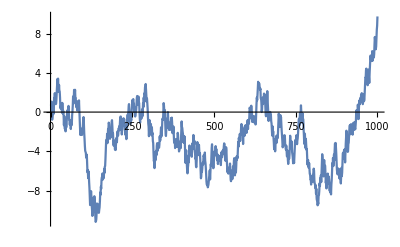

```mathematica
ListLinePlot[Accumulate[RandomReal[{-1,1},1000]]]
```

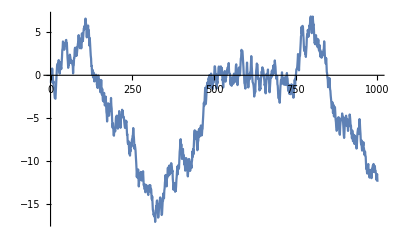

```mathematica
ListLinePlot[Accumulate[RandomReal[{-1,1},1000]]]
```

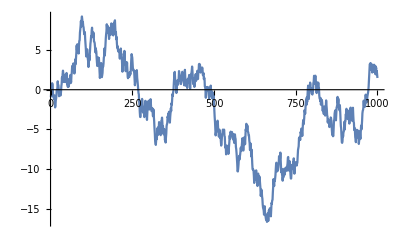
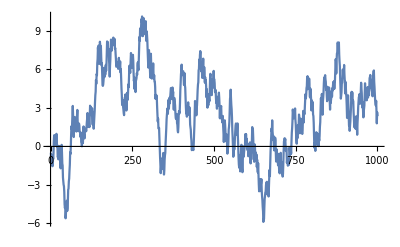
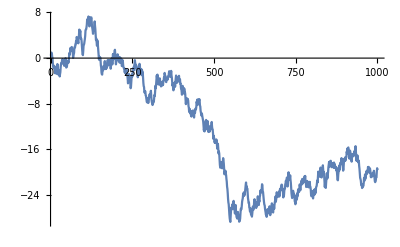
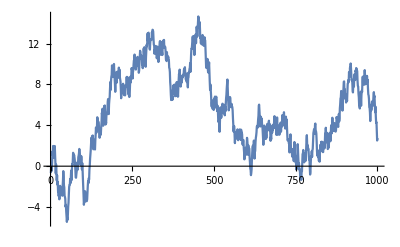
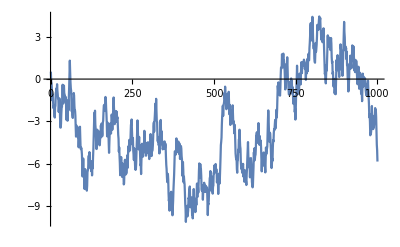
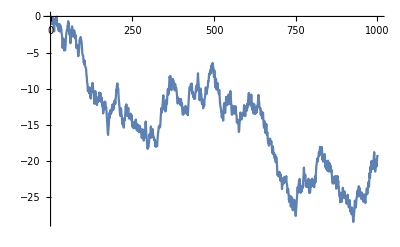
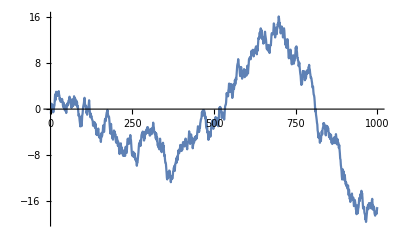
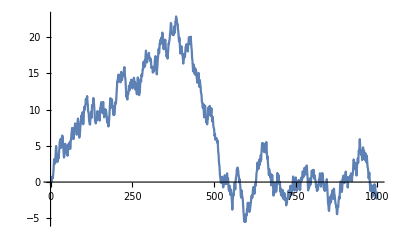

```mathematica
Table[ListLinePlot[Accumulate[RandomReal[{-1,1},1000]]],{i,0,10}]
```

```mathematica
GeoRegionValuePlot[EntityClass["AdministrativeDivision","USCountiesTexas"]->
```

```mathematica
GeoRegionValuePlot[EntityClass["AdministrativeDivision","USCountiesTexas"]->"Population"]
```

-Graphics-

```mathematica
GeoRegionValuePlot[EntityClass["AdministrativeDivision","USCountiesCalifornia"]->"Population"]
```

-Graphics-

```mathematica
GeoEntities[Entity["AdministrativeDivision",{"California","UnitedStates"}], "City"]
```

{Calimesa,Emerald Lake Hills,Sunnyside-Tahoe City,Manton,Pleasant Hill,East San Gabriel,Sutter Creek,Kirkwood,Fowler,Turlock,Oceano,Gold River,Shasta Lake,Mayflower Village,San Buenaventura (Ventura),Saratoga,Selma,Barstow,El Monte,Georgetown,Clovis,Elizabethtown,Beckwourth,La Presa,El Granada,Rancho Palos Verdes,San Marino,Redlands,Twentynine Palms Base,Visalia,Menlo Park,Long Beach,Crestline,Denair,North Lakeport,Baldwin Park,Placerville,Salton Sea Beach,Wildomar,Olivehurst,Signal Hill,Lathrop,Winton,Prattville,Waterford,Laton,Oceanside,Winters,Temelec,Fairfield,Pollock Pines,Shaver Lake,Westmont,Stratford,Fieldbrook,Westmorland,Stockton,Lucerne,Santa Ana,Arden-Arcade,Lakeport,Lost Hills,Palo Cedro,Alpaugh,Delano,Rohnert Park,Corcoran,Rosamond,Valinda,La Habra Heights,Hidden Valley Lake,Commerce,Vine Hill,Round Valley,Santa Venetia,Alturas,Penngrove,Rancho Tehama Reserve,Tustin Foothills,Moreno Valley,Victorville,Stallion Springs,Belden,South San Francisco,Grand Terrace,Angels City,Edwards AFB,North Highlands,Crescent Mills,Sanger,Rancho Cordova,Rancho Santa Margarita,Oxnard,Healdsburg,Fairfax,La Verne,Aromas,Bombay Beach,Citrus,Manhattan Beach,Atascadero,Larkfield-Wikiup,Novato,Palermo,Red Bluff,Alta Sierra,Dorrington,Lemoore,Los Molinos,Rancho Mirage,Rio Dell,Chino Hills,West Modesto,Mendocino,Sand City,Rodeo,Casa de Oro-Mount Helix,Redway,Pearsonville,Fontana,Port Hueneme,South Taft,Lakeland Village,Rancho Calaveras,Auberry,French Camp,Valley Springs,Quartz Hill,Le Grand,San Dimas,Parkway-South Sacramento,Walnut Grove,Torrance,Crescent City North,Cambria,Sedco Hills,Montecito,Moss Landing,East Foothills,Hydesville,Suisun City,Searles Valley,Lake Almanor Country Club,McKittrick,Colton,San Lorenzo,Big River,Raisin City,Sonoma,Talmage,Indio,Kerman,Hesperia,Woodland,Mohawk Vista,Nuevo,Sunol,Los Banos,Beaumont,Bootjack,Foster City,Kensington,Bear Valley Springs,Bethel Island,Concord,768,Fort Jones,Poplar-Cotton Center,Marysville,Dixon Lane-Meadow Creek,Portola Hills,Vincent,Bertsch-Oceanview,Buttonwillow,Burbank,Sunol-Midtown,Orcutt,Moss Beach,Pico Rivera,Vacaville,Imperial Beach,Kettleman City,La Mesa,West Sacramento,Holtville,Independence,Irwindale,Lodi,Brea,Oroville,South San Gabriel,Round Mountain,Vandenberg Village,Camino Tassajara,Santa Clarita,Bodega Bay,Del Aire,Montalvin Manor,Belmont,North El Monte,Camarillo,Pacific Grove,Bayview,Loma Linda,Tamalpais-Homestead Valley,Stinson Beach,Covina,Chinese Camp,Wilkerson,Fellows,Parksdale,Solana Beach,San Fernando,Rio Linda,Tahoe Vista,Graeagle,La Canada Flintridge,Reedley,Challenge-Brownsville,Ducor,Florin,Glendale,Calipatria,San Juan Bautista,Modesto,Lake Wildwood,Valley Ranch,California City,San Miguel,Santee,Frazier Park,Tuolumne City,Tomales,Spring Garden,Canyondam,San Diego Country Estates,Klamath,Hanford,Dos Palos,Prunedale,Homeland,Trinidad,Grass Valley,Carlsbad,Monterey Park,Esparto,Carrick,Shackelford,Tipton,Onyx,Brisbane,Taft Heights,Littlerock,Porterville,Iron Horse,Lockeford,Derby Acres,Ehrenberg,Cayucos,Mariposa,Oakland,Glendora,Cedar Ridge,Aliso Viejo,Malibu,Carmichael,Arnold,Loma Rica,South Oroville,Channel Islands Beach,Graton,Oakley,Yucca Valley,Earlimart,Valley Acres,Watsonville,Durham,Casa Conejo,Piru,West Bishop,Bakersfield,Murrieta,Capitola,Big Bear City,Crescent City,West Menlo Park,Laguna Hills,Sun City,West Covina,Tecopa,Pedley,West Athens,East Palo Alto,Millville,Lakehead-Lakeshore,El Cerrito,Inverness,Lake Forest,East La Mirada,San Ardo,Hollister,Hayward,San Juan Capistrano,March AFB,Muscoy,Clio,Industry,Palm Springs,El Centro,San Mateo,Firebaugh,Yreka,Los Osos,San Jacinto,Chilcoot-Vinton,Florence-Graham,Traver,Mono Vista,Walnut Park,Perris,Diamond Bar,Oakdale,Marina del Rey,Nipomo,West Point,Rosedale,Napa,Arvin,Westhaven-Moonstone,Moorpark}
 |  |  |  |

```mathematica
Plus@@#&
```

Plus@@#1&

```mathematica
(Plus@@#1&)[{a,b,c}]
```

a+b+c

```mathematica
GeoListPlot[{LinguisticAssistant,LinguisticAssistant}]
```

-Graphics-

```mathematica
GeoListPlot@
GeoEntities[Entity["AdministrativeDivision",{"California","UnitedStates"}], "City"]
```

-Graphics-

```mathematica
GeoListPlot[{Entity["Country","Indonesia"],Entity["Country","Malaysia"],Entity["Country","Thailand"],Entity["Country","Vietnam"]}]
```

-Graphics-

```mathematica
GeoListPlot[{DeleteCases[EntityValue[Entity["HistoricalEvent","KoreanWarBegins"],"CountriesInvolved"],Entity["HistoricalCountry",__]]},GeoBackground->"ReliefMap",GeoRange->"World"
]
```

-Graphics-

```mathematica
GeoListPlot[{{LinguisticAssistant,LinguisticAssistant},{LinguisticAssistant,LinguisticAssistant},{LinguisticAssistant,LinguisticAssistant}}]
```

-Graphics-

```mathematica
GeoListPlot[{{Entity["Country","Bulgaria"],Entity["Country","Greece"]},{Entity["Country","Albania"],Entity["Country","Romania"]},{Entity["Country","Turkey"],Entity["Country","Lebanon"]}}]
```

-Graphics-

```mathematica
$MaxMachineNumber
```

1.79769×10^308

```mathematica
x :> y :> z
```

```mathematica
1:>2
```

```mathematica
a:>2
```

a:>2

```mathematica
a+1/.a:>2
```

3

```mathematica
x:>RandomReal[]
```

x:>RandomReal[]

```mathematica
x:>RandomReal[]
```

x:>RandomReal[]

```mathematica
x/.x:>RandomReal[]
```

0.530105

```mathematica
x/.x:>RandomReal[]
```

0.553575

```mathematica
RandomGraph[5]
```

RandomGraph::dist: A graph distribution is expected at position 1 in RandomGraph[5].

RandomGraph[5]

```mathematica
TimeSeriesForecast[ARProcess[{-.2,.4,.6},.1],{.1,.3,-.2,0,-.2,.2},3]
```

0.0752

```mathematica
TimeSeriesForecast[ARProcess[{-.2,.4,.6},.1],{.1,.3,-.2,0,-.2,.2},3]
```

0.0752

```mathematica
GeoListPlot[GeoPosition[37.751,-97.822]]
```

GeoListPlot::ngeoents: GeoPosition[37.751,-97.822] is not a list or nested list of geographical entities

GeoListPlot[GeoPosition[37.751,-97.822]]

```mathematica
GeoListPlot[GeoPosition[{37.751,-97.822}]]
```

-Graphics-

```mathematica
GeoListPlot[{
GeoPosition[{37.751,-97.822}],
GeoPosition[{34.602,-118.231}],
GeoPosition[{37.406,-122.078}],
GeoPosition[{41.295,-96.055}]
}]
```

-Graphics-

```mathematica
GeoListPlot[{
GeoPosition[{37.751,-97.822}],
GeoPosition[{34.602,-118.231}],
GeoPosition[{37.406,-122.078}],
GeoPosition[{41.295,-96.055}]
}, GeoLabels->True]
```

-Graphics-

```mathematica
D[u[x,t],t]==D[u[x,t],x]
```

u^(0,1)[x,t]==u^(1,0)[x,t]

```mathematica
DSolve[Derivative[0,1][u][x,t]==Derivative[1,0][u][x,t],{u[x,t],u[x,t]},{t,x}]
```

{{u[x,t]→C[1][t+x]}}

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[1,0][u][x,t],u[x,0]==PDF[NormalDistribution[],x]},u[x,t],{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(1,0)[x,t],u[x,0]==(ⅇ^(-x^2/2))/(√(2 π))},u[x,t],{t,x}]

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[1,0][u][x,t],u[x,0]==(ⅇ^(-x^2/2))/(√(2 π))},u[x,t],{x,t}]
```

{{u[x,t]→(ⅇ^(-1/2 (t+x)^2))/(√(2 π))}}

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[1,0][u][x,t],u[x,0]==(ⅇ^(-x^2/2))/(√(2 π))},u[x,t],{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(1,0)[x,t],u[x,0]==(ⅇ^(-x^2/2))/(√(2 π))},u[x,t],{t,x}]

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[1,0][u][x,t],u[x,0]==(ⅇ^(-x^2/2))/(√(2 π))},u[x,t],{x,t}]
```

{{u[x,t]→(ⅇ^(-1/2 (t+x)^2))/(√(2 π))}}

```mathematica
Plot3D[(ⅇ^(-1/2 (t+x)^2))/(√(2 π)), {x, -1, 1}, {t, 0, 5}, PlotLegends->"Expressions", ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
Plot3D[
(ⅇ^(-1/2 (t+x)^2))/(√(2 π)),
 {x, -1, 1}, {t, 0, 5}, 
PlotLegends->"Expressions", ColorFunction->"DarkRainbow", AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[
(ⅇ^(-1/2 (t+x)^2))/(√(2 π)),
 {x, -3, 3}, {t, 0, 5}, 
PlotLegends->"Expressions", ColorFunction->"DarkRainbow", AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[
(ⅇ^(-1/2 (t+x)^2))/(√(2 π)),
 {x, -3, 3}, {t, 0, 10}, 
PlotLegends->"Expressions",
 ColorFunction->"DarkRainbow",
 AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[
(ⅇ^(-1/2 (t+x)^2))/(√(2 π)),
 {x, -3, 3}, {t, 0, 8}, 
PlotLegends->"Expressions",
 ColorFunction->"DarkRainbow",
 AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Laplacian[(ⅇ^(-1/2 (t+x)^2))/(√(2 π)),{x,t}]
```

-ⅇ^(-1/2 (t+x)^2) √(2/π)+ⅇ^(-1/2 (t+x)^2) √(2/π) (-t-x)^2

```mathematica
1⊻2
```

1⊻2

```mathematica
1>0⊻2<1
```

True

```mathematica
BinormalDistribution[{0,0},{1,1}]
```

BinormalDistribution[{0,0},{1,1}]

```mathematica
PDF[BinormalDistribution[{0,0},{1,1}],{x,y}]
```

BinormalDistribution::vrposln: The value {0,0} at position 1 in BinormalDistribution[{0,0},{1,1}] is expected to be a length 2 list of positive numbers.

PDF[BinormalDistribution[{0,0},{1,1}],{x,y}]

```mathematica
ParallelTable[Plot3D[PDF[BinormalDistribution[{-1,1},{1,2},ρ],{x,y}],{x,-3,3},{y,-6,6},PlotRange->All,MeshFunctions->{#3&},MeshShading->{None,Red,None,Yellow},PlotPoints->25],{ρ,{-.7,-0.4,0,0.3,0.5,0.8}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
PDF[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ],{x,y}]
```

(ⅇ^(-((x-μ_1)^2/σ_1^2+(y-μ_2)^2/σ_2^2-(2 ρ (x-μ_1) (y-μ_2))/(σ_1 σ_2))/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
(ⅇ^(-((x-Subscript[μ, 1])^2/Subscript[σ, 1]^2+(y-Subscript[μ, 2])^2/Subscript[σ, 2]^2-(2 ρ (x-Subscript[μ, 1]) (y-Subscript[μ, 2]))/(Subscript[σ, 1] Subscript[σ, 2]))/(2 (1-ρ^2))))/(2 π √(1-ρ^2) Subscript[σ, 1] Subscript[σ, 2])
```

```mathematica
ParallelTable[Plot3D[CDF[BinormalDistribution[{-1,1},{1,2},ρ],{x,y}],{x,-3,3},{y,-6,6},MeshFunctions->{#3&},MeshShading->{None,Red,None,Yellow},PlotPoints->25],{ρ,{-.7,-0.5,0,0.3,0.5,0.8}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
sample=RandomVariate[𝒹=BinormalDistribution[{1,2},{1.5,2},0.6],10^4]
```

{{3.30685,6.75471},{0.93872,0.865718},{1.28636,4.54912},{-0.880523,1.36734},9993,{-1.27835,0.340941},{2.30064,2.77262},{2.24304,2.16371}}
 |  |  |  |

```mathematica
{Histogram3D[sample,30,"PDF",ColorFunction->"Rainbow",PlotRange->{{-5,6},{-3,7},All}],Plot3D[PDF[𝒹,{x,y}],{x,-5,6},{y,-3,7},ColorFunction->"Rainbow",PlotPoints->35,PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
{Histogram3D[sample,30,"PDF",ColorFunction->"Rainbow",PlotRange->{{-5,6},{-3,7},All}],Plot3D[PDF[𝒹,{x,y}],{x,-5,6},{y,-3,7},ColorFunction->"DarkRainbow",PlotPoints->35,PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Skewness[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ]]
```